```mathematica
A2[z_]:=Module[{firstSum,secondSum},firstSum=Total[z[[;;,1;;3]]^2,{2}];
secondSum=Total[z[[;;,4;;15]]^2,{2}];
(-firstSum+secondSum)/10*(2/Sqrt[5])];
(*Computes the autocorrelation function (ACF) up to maxLag*)
ClearAll[autocorrelationFunction]
autocorrelationFunction[data_List,maxLag_Integer?NonNegative]:=Module[{n,meanData,varData},n=Length[data];
meanData=Mean[data];
varData=Variance[data];
Table[If[k==0,1,Total[(data[[1;;n-k]]-meanData) (data[[k+1;;n]]-meanData)]/(n-k)/varData],{k,0,maxLag}]];

(*Computes the integrated autocorrelation time from the ACF*)
ClearAll[integratedAutocorrelationTime]
integratedAutocorrelationTime[data_List,maxLag_Integer]:=Module[{acfVals,posSum=0},acfVals=autocorrelationFunction[data,maxLag];
Do[If[acfVals[[k+1]]>0,posSum+=acfVals[[k+1]],Break[]],{k,1,maxLag}];
1+2 posSum];

(*Global initialization function to define key variables*)
Init[]:=Module[{zRaw,shift,phiRaw,params},(*Set working directory to the parent of the notebook's directory*)SetDirectory[ParentDirectory[DirectoryName[NotebookFileName[]]]];(*Import z data and convert each pair of entries to a complex number*)zRaw=Import["output/z_history.dat"];
z=Map[(#1[[1]]+#1[[2]]*I)&,zRaw];
Dz=Import["data/initial_x.dat"][[1,1]]-1;
z=Partition[z,Dz];phiRaw=Import["output/phi_history.dat"];
phi=Map[(#1[[1]]+I*#1[[2]])&,phiRaw];
(*Global variables (z,shiftz,phi,d0,t0,t1,binn,bwParams,w,wa) are now defined*)Null];
```

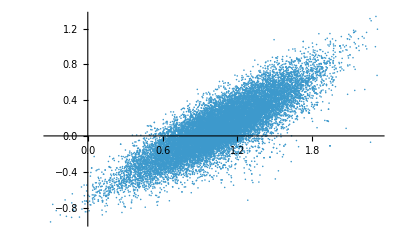

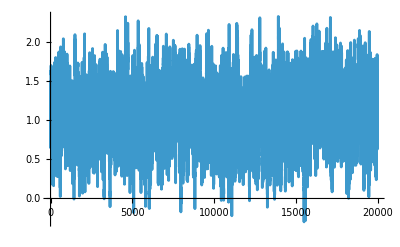

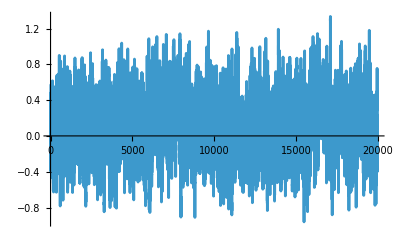

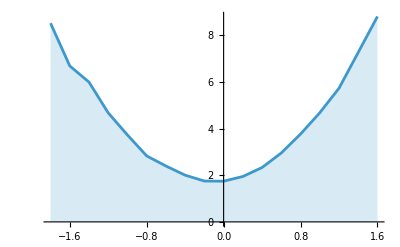

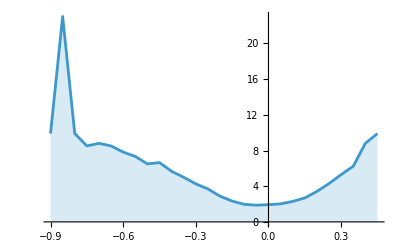

0.281799

12.5928

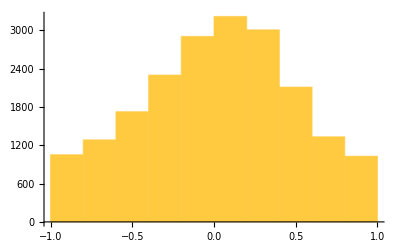

12.1643

```mathematica
Init[];
(*Import Data*)data=Import["output/virial.dat"];
ListPlot[data,PlotRange->All]
ListPlot[data[[;;,1]],Joined->True,PlotRange->All]
ListPlot[data[[;;,2]],Joined->True,PlotRange->All]
pca=PrincipalComponents[data];
fData=pca[[All,1]];
hist=HistogramList[fData,{0.2}]; (*adjust bin width*)
prob=N[hist[[2]]/Total[hist[[2]]]];
freeEnergy=-Log[prob+10^-10]; (*avoid log(0)*)
ListLinePlot[Transpose[{hist[[1, ;;-2]],freeEnergy}],Filling->Axis,PlotRange->All]
fData=pca[[All,2]];
hist=HistogramList[fData,{0.05}]; (*adjust bin width*)
prob=N[hist[[2]]/Total[hist[[2]]]];
freeEnergy=-Log[prob+10^-10]; (*avoid log(0)*)
ListLinePlot[Transpose[{hist[[1, ;;-2]],freeEnergy}],Filling->Axis,PlotRange->All]
Abs[Mean[phi]]
1/Abs[Mean[phi]]^2
Histogram[Arg[phi]/Pi,{-1,1,0.2},PlotRange->{{-1,1},Automatic}]
integratedAutocorrelationTime[data[[;;,1]],10]
```